```mathematica
(*PARAMETERS*)
n = 6; (* Number of nodes *)
p = .1; (* Probability of small world connection *)
```

```mathematica
(* Logistic Function *)
logi[x_] := x^2 - x
```

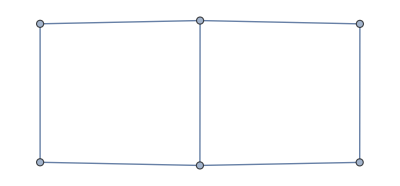

```mathematica
(* Define Small-Worldesque graph *)
A = ConstantArray[0,{n,n}];
Do[ A[[i,j]]  = If[i<j , RandomChoice[{p,1-p}->{1,0}],0],{i,n},{j,n}];
A = ReplacePart[A,{i_,j_} /; j == i+1  ->1];
A[[1,n]] = 1;
A = A + Transpose[A];
AdjacencyGraph[A]
```

```mathematica
G  = Graph[AdjacencyGraph[A]];
Specialize[G,{1,2,3}]
```

IndexGraph::graph: A graph object is expected at position 1 in IndexGraph[{1 -> 2, 2 -> 1, 2 -> 3, 3 -> 2, 10 -> 11, 11 -> 10, 11 -> 12, 12 -> 11, 1 -> 12, 10 -> 3, 16 -> 17, 17 -> 16, 17 -> 18, 18 -> 17, 1 -> 18, 18 -> 1, 22 -> 23, 23 -> 22, 23 -> 24, 24 -> 23, 1 -> 24, 24 -> 3, 28 -> 29, 29 -> 28, 29 -> 30, 30 -> 29, 3 -> 28, 28 -> 3, 34 -> 35, 35 -> 34, 35 -> 36, 36 -> 35, 3 -> 34, 36 -> 1, 40 -> 41, 41 -> 40, 41 -> 42, 42 -> 41, 3 -> 40, 42 -> 3, 46 -> 47, 47 -> 46, 47 -> 48, 48 -> 47, 3 -> 48, 46 -> 3, 52 -> 53, 53 -> 52, 53 -> 54, 54 -> 53, « 8 »}].

IndexGraph[{1->2,2->1,2->3,3->2,10->11,11->10,11->12,12->11,1->12,10->3,16->17,17->16,17->18,18->17,1->18,18->1,22->23,23->22,23->24,24->23,1->24,24->3,28->29,29->28,29->30,30->29,3->28,28->3,34->35,35->34,35->36,36->35,3->34,36->1,40->41,41->40,41->42,42->41,3->40,42->3,46->47,47->46,47->48,48->47,3->48,46->3,52->53,53->52,53->54,54->53,3->54,54->1,58->59,59->58,59->60,60->59,3->60,60->3}]